```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

```mathematica
<<NDSolve`FEM`
```

# Core Routines

## Importing data

```mathematica
(*numerical solution, flag == 0,
 exact solution, flag == 1 and 
error flag == 2
error velocity space flag == 3
fe index distribution flag == 4
convergence table flag == 5*)
importdata[dof_,p_,refinetype_,flag_,outputdir_]:=Module[{result,filename},
Which[flag == 0,
filename=StringJoin["../",outputdir,"/solution/numerical_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 1,
filename=StringJoin["../",outputdir,"/solution/exact_solution",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],

flag == 2,
filename=StringJoin["../",outputdir,"/solution/error",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 3,
filename=StringJoin["../",outputdir,"/solution/error_velocity_space",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 4,
filename=StringJoin["../",outputdir,"/solution/fe_index",refinetype,"degree_",ToString[p],"_DOF_",ToString[dof]],
flag == 5,
filename=StringJoin["../",outputdir,"/convergence_tables/convergence_table",refinetype,"degree_",ToString[p]]
];

Print[Style["Reading Data from...",FontColor->Black]];
Print[Style[ToString[filename],FontColor->Green]];
result = Import[filename,"Table"]⟦2;;-1,All⟧
]
```

## IDs for different variables

```mathematica
(*we declare the IDs for different variables, this will help us with plotting*)
IDRho = 1+2;
IDvx = 2+2;
IDvy = 3+2;
IDtheta = 4+2;
IDsigmaxx = 5+2;
IDsigmaxy = 6+2;
IDsigmayy = 7+2;
IDqx = 8+2;
IDqy = 9+2;
```

## Mapping to Primitive variables

```mathematica
(*we change the numerical solution obtained to the primitive variables.*)
ConvToPrim[sol_]:=Module[{factorθ,factorσ,factorq,trialsol},
trialsol = sol;
factorθ = -√(2/3);
factorσ = √2;
factorq = -√(5/2);
trialsol⟦All,IDtheta⟧ =factorθ * sol⟦All,IDtheta⟧;
trialsol⟦All,{IDqx,IDqy}⟧ =factorq*sol⟦All,{IDqx,IDqy}⟧;
trialsol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmayy}⟧=factorσ*sol⟦All,{IDsigmaxx,IDsigmaxy,IDsigmayy}⟧;

trialsol
]
```

## Plotting help

### Reading the mesh

```mathematica
(*In the following function we read the gmsh file*)
ReadMeshFile[filename_]:=Import[filename,"Table"];

(*In the following function we extract the coordinates for the vertices*)
ExtractVertices[mesh_]:=Module[{nVerts,verts,offset},
(*offset from the gmsh *)
offset = 5;

(*total number of vertices in the mesh*)
nVerts = mesh⟦offset⟧⟦1⟧;

(*vertices of the mesh*)
verts = mesh⟦offset+1;;offset+nVerts,All⟧;

(*now we only extract the coordinates*)
verts⟦All,2;;-1⟧
]

(*In the following function we extract the elements*)
ExtractElements[mesh_]:=Module[{nElm,Elm,beginElm,beginQuads,offset},
(*location where the elements begin*)
beginElm = Position[mesh,"$Elements"]⟦1,1⟧;

(*Extract all the elements. This includes the physical groups which were defined during the mesh generation*)
Elm=mesh⟦beginElm;;-1,All⟧;

(*location where the actual quads begin, 3 because of the offset and 4 because that stores the ID of the physical entity.
The value 3 in the checks whether we have a quad or not.
*)
offset = 3;
Do[If[Length[Elm⟦ii⟧]≥5,If[Elm⟦ii⟧⟦2⟧==3,beginQuads=ii; Break[];Print["Inside"];]],{ii,1,Length[Elm]}];

(*from begin quads to -2 because the last element in $EndElements*)
Elm = Elm⟦beginQuads;;-2,6;;-1⟧;

Elm
]

(*In the following routine we check the mesh which we have read from the file*)
CheckElms[Elms_,nVerts_]:=Module[{},

(*We check whether all the vertices have been included or not in the connectivity data*)

If[Norm[DeleteDuplicates[Sort[Flatten[Elms]]]-Range[1,nVerts]]==0,Print[Style["Correct Mesh",FontColor->Green]],Print[Style["InCorrect Mesh",FontColor->Red]]]
];


CreateMesh[mesh_,dim_]:=Module[{Verts,Elms,OrderedVerts,nVerts,finalMesh},

Verts = ExtractVertices[mesh]⟦All,1;;dim⟧;
nVerts = Length[Verts];
Elms = ExtractElements[mesh];

CheckElms[Elms,nVerts];
finalMesh = ToElementMesh["Coordinates"->Verts,"MeshElements"->{QuadElement[Elms]},"MeshOrder"->3];

finalMesh
]
```

### Interpolation

```mathematica
InterpolateSolution[solution_]:=Module[{densityData,vxData,vyData,thetaData,sigmaxxData,sigmaxyData,sigmayyData,qxData,qyData,pressureData,densityValue},

(*convert data into a format which is read by Interpolation*)
densityData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDRho⟧},{ii,1,Length[solution]}];

vxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDvx⟧},{ii,1,Length[solution]}];

vyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDvy⟧},{ii,1,Length[solution]}];

thetaData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDtheta⟧},{ii,1,Length[solution]}];

(*sigmaxxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmaxx⟧},{ii,1,Length[solution]}];

sigmaxyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmaxy⟧},{ii,1,Length[solution]}];

sigmayyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDsigmayy⟧},{ii,1,Length[solution]}];

qxData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDqx⟧},{ii,1,Length[solution]}];

qyData = Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDqy⟧},{ii,1,Length[solution]}];

pressureData=Table[{solution⟦ii,{1,2}⟧,solution⟦ii,IDtheta⟧+solution⟦ii,IDRho⟧},{ii,1,Length[solution]}];*)

(*remove the duplicate entries for Interpolation function*)
densityData = DeleteDuplicatesBy[densityData,First];
vxData = DeleteDuplicatesBy[vxData,First];
vyData = DeleteDuplicatesBy[vyData,First];
thetaData = DeleteDuplicatesBy[thetaData,First];
(*sigmaxxData = DeleteDuplicatesBy[sigmaxxData,First];
sigmaxyData = DeleteDuplicatesBy[sigmaxyData,First];
sigmayyData = DeleteDuplicatesBy[sigmayyData,First];
qxData = DeleteDuplicatesBy[qxData,First];
qyData = DeleteDuplicatesBy[qyData,First];
pressureData=DeleteDuplicatesBy[pressureData,First];*)

(*we first need to compute the value of the solution a the mesh points*)
(*densityData=Interpolation[densityData,InterpolationOrder->1];
densityValue = densityData[0,Sequence@@#]&/@coords;*)

densityData=Interpolation[densityData,InterpolationOrder->1];
vxData=Interpolation[vxData,InterpolationOrder->1];
vyData=Interpolation[vyData,InterpolationOrder->1];
thetaData=Interpolation[thetaData,InterpolationOrder->1];
(*sigmaxxData=Interpolation[sigmaxxData,InterpolationOrder->1];
sigmaxyData=Interpolation[sigmaxyData,InterpolationOrder->1];
sigmayyData=Interpolation[sigmayyData,InterpolationOrder->1];
qxData=Interpolation[qxData,InterpolationOrder->1];
qyData=Interpolation[qyData,InterpolationOrder->1];
pressureData=Interpolation[pressureData,InterpolationOrder->1];*)

{densityData,vxData,vyData,thetaData,sigmaxxData,sigmaxyData,sigmayyData,qxData,qyData,pressureData}
]
```

### Plot Contour

```mathematica
PlotContour[data_,domain_,ratio_,range_]:=Module[{label},

label={Style["x",FontSize->14],Style["y",FontSize->14],None,None};

ContourPlot[data,{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],ContourLines->False,Contours->10,PlotRange->All,ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->Large,AspectRatio->1/ratio,ContourLabels->False,Frame->True,FrameTicksStyle->{16,16},FrameLabel->label,RotateLabel->False,Exclusions->None]

]
```

### Plot Streamlines

```mathematica
PlotStreamlines[data_,domain_,ratio_,range_]:=Module[{},
StreamPlot[{Sum[(data⟦ii,1⟧[x,y])/Length[data],{ii,1,Length[data]}],Sum[(data⟦ii,2⟧[x,y])/Length[data],{ii,1,Length[data]}]},{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],PlotRange->{Full,Full},PlotLegends->None,AspectRatio->1/ratio,StreamStyle->Green,StreamPoints->{Automatic,0.05},ImageSize->Large]]
```

### Plot Vector

```mathematica
PlotVectorlines[data_,domain_,ratio_,range_]:=Module[{},
VectorPlot[{Sum[(data⟦ii,1⟧[x,y])/Length[data],{ii,1,Length[data]}],Sum[(data⟦ii,2⟧[x,y])/Length[data],{ii,1,Length[data]}]},{x,range⟦1,1⟧,range⟦1,2⟧},{y,range⟦2,1⟧,range⟦2,2⟧},
RegionFunction->Function[{x,y},RegionMember[domain,{x,y}]],PlotRange->{Full,Full},ColorFunction->Hue,PlotLegends->Automatic,AspectRatio->1/ratio,VectorPoints->30,ImageSize->Large,VectorScale->0.05]]
```

### Sort Solution

### Scale Dofs

```mathematica
(*dataa is the convergence table from dealii and dim is the number of dimensions*)
ScaleDofs[data_,dim_]:=Module[{columnDof,temp},

(*the column at which the dofs are stored*)
columnDof = 5;
temp = data;
temp⟦All,columnDof⟧=Power[data⟦All,columnDof⟧,1/dim];
temp
]
```

### Exact Order

```mathematica
(*Given the end points along the x-coordinate and the y -coordinate of the starting point we find the y *)
ExactOrder[x_,y_,slope_]:=Module[{y2,x1,x2,y1},
x1 = x⟦1⟧;
x2 = x⟦2⟧;
y1 = y;

y2=Exp[Log[y1]- slope*(Log[x1]-Log[x2])];

N[{{x1,y1},{x2,y2}}]
]
```

# Results

## Solution Poisson Heat Conduction

### Reference Solution

```mathematica
exactKn0p1 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactKn0p3 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactKn0p5 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];

(*fix for the wall temperature*)
exactKn0p1⟦All,4⟧+=1;
exactKn0p3⟦All,4⟧+=1;
exactKn0p5⟦All,4⟧+=1;

θExactKn0p1=Interpolation[exactKn0p1⟦All,{1,4}⟧];
σExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,6}⟧];
qExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,7}⟧];

θExactKn0p3=Interpolation[exactKn0p3⟦All,{1,4}⟧];
σExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,6}⟧];
qExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,7}⟧];

θExactKn0p5=Interpolation[exactKn0p5⟦All,{1,4}⟧];
σExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,6}⟧];
qExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,7}⟧];
```

```mathematica
θExactKn0p3[x]
```

InterpolatingFunction[{{-0.5, 0.5}}, <>][x]

### G20

```mathematica
ndof={2600,5200,7800,10400};
polyDegree = 1;
dimension=2;
```

#### Char Boundary Implementation

```mathematica
foldername = "Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_CharBC";
Do[numsol20CharBC[ii]=importdata[ndof⟦ii⟧,polyDegree,"_global_",0,foldername],{ii,1,Length[ndof]}];
Do[numsol20CharBC[ii] = ConvToPrim[numsol20CharBC[ii]],{ii,1,Length[ndof]}];
```

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_CharBC/solution/numerical_solution_global_degree_1_DOF_2600

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_CharBC/solution/numerical_solution_global_degree_1_DOF_5200

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_CharBC/solution/numerical_solution_global_degree_1_DOF_7800

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_CharBC/solution/numerical_solution_global_degree_1_DOF_10400

```mathematica
Do[solution20CharBC[ii] = InterpolateSolution[numsol20CharBC[ii]],{ii,1,Length[ndof]}];
```

```mathematica
ConvergenceTable20CharBC=importdata[ndof⟦1⟧,polyDegree,"_global_",5,foldername];
ConvergenceTable20CharBC=ScaleDofs[ConvergenceTable20CharBC,dimension];
```

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_CharBC/convergence_tables/convergence_table_global_degree_1

#### Odd Boundary Implementation

```mathematica
foldername = "Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_OddBC";
Do[numsol20OddBC[ii]=importdata[ndof⟦ii⟧,polyDegree,"_global_",0,foldername],{ii,1,Length[ndof]}];
Do[numsol20OddBC[ii] = ConvToPrim[numsol20OddBC[ii]],{ii,1,Length[ndof]}];
```

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_OddBC/solution/numerical_solution_global_degree_1_DOF_2600

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_OddBC/solution/numerical_solution_global_degree_1_DOF_5200

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_OddBC/solution/numerical_solution_global_degree_1_DOF_7800

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_OddBC/solution/numerical_solution_global_degree_1_DOF_10400

```mathematica
Do[solution20OddBC[ii] = InterpolateSolution[numsol20OddBC[ii]],{ii,1,Length[ndof]}];
```

```mathematica
ConvergenceTable20OddBC=importdata[ndof⟦1⟧,polyDegree,"_global_",5,foldername];
ConvergenceTable20OddBC=ScaleDofs[ConvergenceTable20OddBC,dimension];
```

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_OddBC/convergence_tables/convergence_table_global_degree_1

#### Kinetic Boundary Implementation

```mathematica
foldername = "Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_KineticBC";
Do[numsol20KineticBC[ii]=importdata[ndof⟦ii⟧,polyDegree,"_global_",0,foldername],{ii,1,Length[ndof]}];
Do[numsol20KineticBC[ii] = ConvToPrim[numsol20KineticBC[ii]],{ii,1,Length[ndof]}];
```

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_KineticBC/solution/numerical_solution_global_degree_1_DOF_2600

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_KineticBC/solution/numerical_solution_global_degree_1_DOF_5200

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_KineticBC/solution/numerical_solution_global_degree_1_DOF_7800

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_KineticBC/solution/numerical_solution_global_degree_1_DOF_10400

```mathematica
Do[solution20KineticBC[ii] = InterpolateSolution[numsol20KineticBC[ii]],{ii,1,Length[ndof]}];
```

```mathematica
ConvergenceTable20KineticBC=importdata[ndof⟦1⟧,polyDegree,"_global_",5,foldername];
ConvergenceTable20KineticBC=ScaleDofs[ConvergenceTable20KineticBC,dimension];
```

Reading Data from...

../Tests/build/output_N6_poisson_heat_conduction_2D_Kn0p1_KineticBC/convergence_tables/convergence_table_global_degree_1

#### Entropy Dissipation Rate

```mathematica
DissipationG20Char = Import["../Tests/build/Entropy_Dissipation_Rate_G20/Entropy_Dissipation_G20_Char","Table"];
DissipationG20Odd = Import["../Tests/build/Entropy_Dissipation_Rate_G20/Entropy_Dissipation_G20_Odd","Table"];
DissipationG20Kinetic = Import["../Tests/build/Entropy_Dissipation_Rate_G20/Entropy_Dissipation_G20_Kinetic","Table"];
```

### G56

```mathematica
ndof={6800,13600,20400,27200};
polyDegree = 1;
dimension=2;
```

#### Char Boundary Implementation

```mathematica
foldername = "Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_CharBC";
Do[numsol56CharBC[ii]=importdata[ndof⟦ii⟧,polyDegree,"_global_",0,foldername],{ii,1,Length[ndof]}];
Do[numsol56CharBC[ii] = ConvToPrim[numsol56CharBC[ii]],{ii,1,Length[ndof]}];
```

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_CharBC/solution/numerical_solution_global_degree_1_DOF_6800

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_CharBC/solution/numerical_solution_global_degree_1_DOF_13600

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_CharBC/solution/numerical_solution_global_degree_1_DOF_20400

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_CharBC/solution/numerical_solution_global_degree_1_DOF_27200

```mathematica
Do[solution56CharBC[ii] = InterpolateSolution[numsol56CharBC[ii]],{ii,1,Length[ndof]}];
```

```mathematica
ConvergenceTable56CharBC=importdata[ndof⟦1⟧,polyDegree,"_global_",5,foldername];
ConvergenceTable56CharBC=ScaleDofs[ConvergenceTable56CharBC,dimension];
```

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_CharBC/convergence_tables/convergence_table_global_degree_1

#### Odd Boundary Implementation

```mathematica
foldername = "Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_OddBC";
Do[numsol56OddBC[ii]=importdata[ndof⟦ii⟧,polyDegree,"_global_",0,foldername],{ii,1,Length[ndof]}];
Do[numsol56OddBC[ii] = ConvToPrim[numsol56OddBC[ii]],{ii,1,Length[ndof]}];
```

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_OddBC/solution/numerical_solution_global_degree_1_DOF_6800

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_OddBC/solution/numerical_solution_global_degree_1_DOF_13600

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_OddBC/solution/numerical_solution_global_degree_1_DOF_20400

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_OddBC/solution/numerical_solution_global_degree_1_DOF_27200

```mathematica
Do[solution56OddBC[ii] = InterpolateSolution[numsol56OddBC[ii]],{ii,1,Length[ndof]}];
```

```mathematica
ConvergenceTable56OddBC=importdata[ndof⟦1⟧,polyDegree,"_global_",5,foldername];
ConvergenceTable56OddBC=ScaleDofs[ConvergenceTable56OddBC,dimension];
```

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_OddBC/convergence_tables/convergence_table_global_degree_1

#### Kinetic Boundary Implementation

```mathematica
foldername = "Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_KineticBC";
Do[numsol56KineticBC[ii]=importdata[ndof⟦ii⟧,polyDegree,"_global_",0,foldername],{ii,1,Length[ndof]}];
Do[numsol56KineticBC[ii] = ConvToPrim[numsol56KineticBC[ii]],{ii,1,Length[ndof]}];
```

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_KineticBC/solution/numerical_solution_global_degree_1_DOF_6800

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_KineticBC/solution/numerical_solution_global_degree_1_DOF_13600

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_KineticBC/solution/numerical_solution_global_degree_1_DOF_20400

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_KineticBC/solution/numerical_solution_global_degree_1_DOF_27200

```mathematica
Do[solution56KineticBC[ii] = InterpolateSolution[numsol56KineticBC[ii]],{ii,1,Length[ndof]}];
```

```mathematica
ConvergenceTable56KineticBC=importdata[ndof⟦1⟧,polyDegree,"_global_",5,foldername];
ConvergenceTable56KineticBC=ScaleDofs[ConvergenceTable56KineticBC,dimension];
```

Reading Data from...

../Tests/build/output_N12_poisson_heat_conduction_2D_Kn0p1_KineticBC/convergence_tables/convergence_table_global_degree_1

### Physical Accuracy

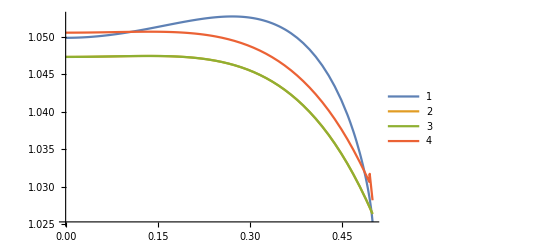

```mathematica
Plot[{θExactKn0p1[x],solution20CharBC[4]⟦IDtheta-2⟧[0,x],solution20OddBC[4]⟦IDtheta-2⟧[0,x],solution20KineticBC[4]⟦IDtheta-2⟧[0,x]},{x,0,0.5},PlotLegends->Automatic]
```

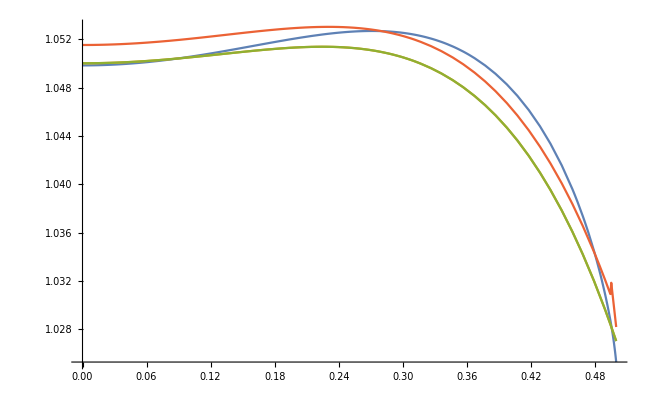

```mathematica
Plot[{θExactKn0p1[x],solution56CharBC[4]⟦IDtheta-2⟧[0,x],solution56OddBC[4]⟦IDtheta-2⟧[0,x],solution56KineticBC[4]⟦IDtheta-2⟧[0,x]},{x,0,0.5},PlotRange->Full]
```

```mathematica
ndof={2600,5200,7800,10400};
errorOddG20 = Quiet[Table[Sqrt[NIntegrate[(θExactKn0p1[x]-solution20OddBC[ii]⟦IDtheta-2⟧[0,x])^2,{x,-0.5,0.5}]],{ii,1,Length[ndof]}]];

errorCharG20 = Quiet[Table[Sqrt[NIntegrate[(θExactKn0p1[x]-solution20CharBC[ii]⟦IDtheta-2⟧[0,x])^2,{x,-0.5,0.5}]],{ii,1,Length[ndof]}]];

ndof={6800,13600,20400,27200};

errorOddG56 = Quiet[Table[Sqrt[NIntegrate[(θExactKn0p1[x]-solution56OddBC[ii]⟦IDtheta-2⟧[0,x])^2,{x,-0.5,0.5}]],{ii,1,Length[ndof]}]];

errorCharG56 = Quiet[Table[Sqrt[NIntegrate[(θExactKn0p1[x]-solution56CharBC[ii]⟦IDtheta-2⟧[0,x])^2,{x,-0.5,0.5}]],{ii,1,Length[ndof]}]];
```

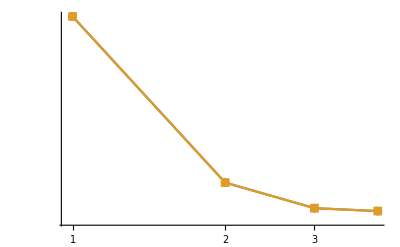

```mathematica
ListLogLogPlot[{errorOddG20,errorCharG20},Joined->True,PlotMarkers->Automatic]
```

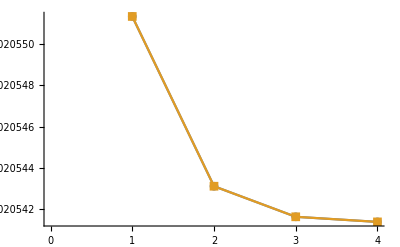

```mathematica
ListPlot[{errorOddG56,errorCharG56},Joined->True,PlotMarkers->Automatic]
```

```mathematica
errorCharG20-errorOddG20
```

{-9.79154×10^-11,0.,0.,0.}

### Convergence Rates

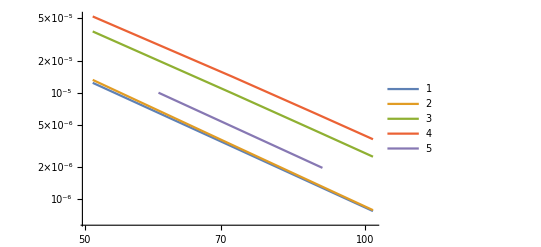

```mathematica
ListLogLogPlot[{ConvergenceTable20CharBC⟦All,{5,1}⟧,ConvergenceTable20OddBC⟦All,{5,1}⟧,ConvergenceTable20CharBC⟦All,{5,3}⟧,ConvergenceTable20OddBC⟦All,{5,3}⟧,ExactOrder[{60,90},10^-5,-4]},Joined->True,PlotLegends->Automatic]
```

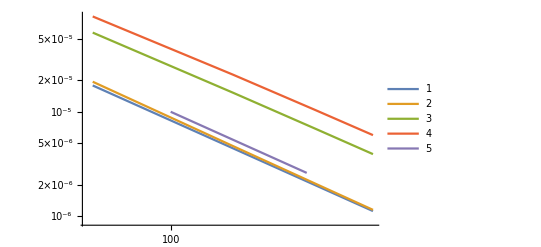

```mathematica
ListLogLogPlot[{ConvergenceTable56CharBC⟦All,{5,1}⟧,ConvergenceTable56OddBC⟦All,{5,1}⟧,ConvergenceTable56CharBC⟦All,{5,3}⟧,ConvergenceTable56OddBC⟦All,{5,3}⟧,ExactOrder[{100,140},10^-5,-4]},Joined->True,PlotLegends->Automatic]
```

### Entropy Dissipation Rate

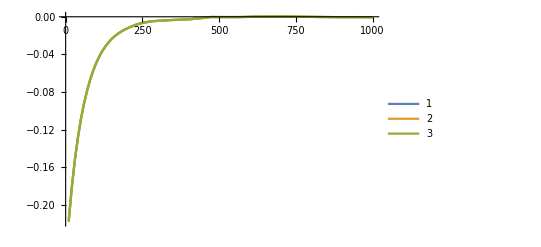

```mathematica
ListPlot[{DissipationG20Char,DissipationG20Odd,DissipationG20Kinetic},Joined->True,PlotLegends->Automatic,PlotRange->Full]
```